```mathematica
solver[a_,b_,n_,α_,β_]:=(
h=(b-a)/n;
a1[x_]:=1;
a2[x_]:=2;
a3[x_]:=5;
f[x_]:=6 Cos[2 x]-7Sin[2 x];
Table[p[i]=6 a1[a+i h]-3h a2[a+i h]+h^2 a3[a+i h],{i,0,n}];
Table[q[i]=-12 a1[a+i h]+4 h^2 a3[a+i h],{i,0,n}];
Table[r[i]=6 a1[a+i h]+3h a2[a+i h]+h^2 a3[a+i h],{i,0,n}];
Table[eq[i]=p[i]c[i-1]+q[i]c[i]+r[i]c[i+1]==6(h^2 f[a+i h]),{i,1,n-1}];
eq[0]=(q[0]-4 p[0])c[0]+(r[0]-p[0])c[1]==6(h^2 f[a]-α p[0]);
eq[n]=(p[n]-r[n])c[n-1]+(q[n]-4r[n])c[n]==6(h^2 f[b]-β r[n]);
sol=Table[c[k],{k,0,n}]/.NSolve[Table[eq[i],{i,0,n}],Table[c[k],{k,0,n}]];
coef=sol[[1]];
For[i=0,i≤n,i++,t[i]=coef[[i+1]]];
t[-1]=6 α-t[1]-4t[0];
t[n+1]=6 β-t[n-1]-4t[n];
Table[B[i][x_]:=Piecewise[{{0,x<a+(i-2) h},{(x-(a+(i-2)h))^3/(6 h^3),a+(i-2)h≤x<a+(i-1)h},{(-3(x-(a+(i-1)h))^3+3h(x-(a+(i-1)h))^2+3 h^2(x-(a+(i-1)h))+h^3)/(6 h^3),a+(i-1)h≤x<a+i h},{(3(x-(a+(i+1)h))^3+3h(x-(a+(i+1)h))^2-3 h^2(x-(a+(i+1)h))+h^3)/(6 h^3),a+i h≤x<a+(i+1)h},{(-(x-(a+(i+2)h))^3)/(6 h^3),a+(i+1)h≤x<a+(i+2)h},{0,x≥a+(i+2)h }}],{i,-1,n+1}];
y[x_]:=Sum[B[i][x]t[i],{i,-1,n+1}];
Clear[p,q,r,eq,sol,coef];
);
```

```mathematica
solver[0,π/4,2,4,1]
```

{Null}

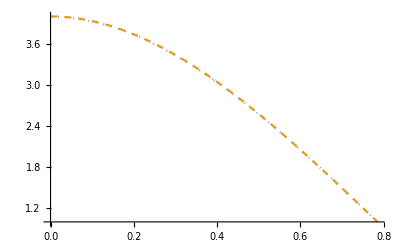

```mathematica
Plot[{y[x],2(1+ⅇ^-x)Cos[2x]+Sin[2x]},{x,0,π/4},PlotStyle->{Dotted,Dashed}]
```

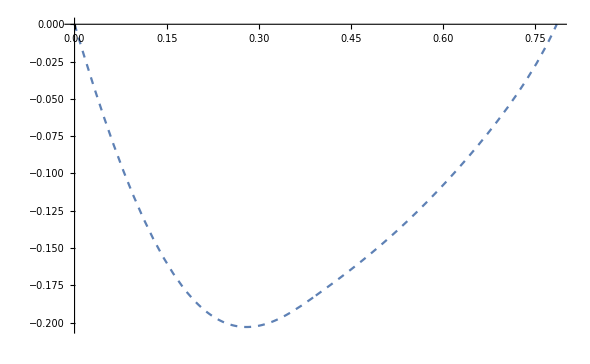

```mathematica
Plot[(y[x]-(2(1+ⅇ^-x)Cos[2x]+Sin[2x]))/(2(1+ⅇ^-x)Cos[2x]+Sin[2x])100,{x,0,π/4},PlotStyle->{Dotted,Dashed}]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
solverHO[R_,n_,α_,λ_,ϵ_]:=(
y0=1;
h=R/(n+1);
a=h;
a1[x_]:=1;
a2[x_]:=1/x;
a3[x_]:=-x^2-λ x^4+ϵ;
f[x_]:=0;
(*eq[1]=c[0]==3/2 α-c[1]/2;
eq[0]=(2/3 ϵ h^2-6)c[0]+(6+(ϵ h^2)/3) c[1]==0;*)
eq[-1]=c[-1]+4 c[0]+c[1]==6y0(1-(a3[0] h^2)/6);
Table[p[i]=6 a1[a+i h]-3h a2[a+i h]+h^2 a3[a+i h],{i,0,n}];
Table[q[i]=-12 a1[a+i h]+4 h^2 a3[a+i h],{i,0,n}];
Table[r[i]=6 a1[a+i h]+3h a2[a+i h]+h^2 a3[a+i h],{i,0,n}];
Table[eq[i]=p[i]c[i-1]+q[i]c[i]+r[i]c[i+1]==0,{i,0,n}];
eq[n+1]=(-R/6+1/(2h))c[n-1]-(2R)/3 c[n]-(R/6+1/(2 h))c[n+1]==0;
sol=Table[c[k],{k,-1,n+1}]/.NSolve[Table[eq[i],{i,-1,n+1}],Table[c[k],{k,-1,n+1}]];
coef=sol[[1]];
For[i=-1,i≤n+1,i++,t[i]=coef[[i+2]]];
(*t[-1]=t[1];*)
Table[B[i][x_]:=Piecewise[{{0,x<a+(i-2) h},{(x-(a+(i-2)h))^3/(6 h^3),a+(i-2)h≤x<a+(i-1)h},{(-3(x-(a+(i-1)h))^3+3h(x-(a+(i-1)h))^2+3 h^2(x-(a+(i-1)h))+h^3)/(6 h^3),a+(i-1)h≤x<a+i h},{(3(x-(a+(i+1)h))^3+3h(x-(a+(i+1)h))^2-3 h^2(x-(a+(i+1)h))+h^3)/(6 h^3),a+i h≤x<a+(i+1)h},{(-(x-(a+(i+2)h))^3)/(6 h^3),a+(i+1)h≤x<a+(i+2)h},{0,x≥a+(i+2)h }}],{i,-1,n+1}];
y[x_]:=Sum[B[i][x]t[i],{i,-1,n+1}];
(*Plot[y[x],{x,0,R},PlotRange->Full]*)
ϕ=Table[{h i,1/6 t[i-1]+2/3 t[i]+1/6 t[i+1]},{i,0,n}];
(*ClearAll[a,h,a1,a2,a3,f,eq,t];*)
)
```

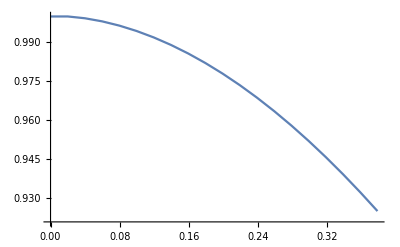

```mathematica
solverHO[6,300,1,0.01,2.021]
ListLinePlot[Table[{ϕ[[i,1]],ϕ[[i,2]]},{i,1,20}],PlotRange->Full]
```

```mathematica
ψ=ⅇ^(-ω/2 x^2)
```

ⅇ^(-(x^2 ω)/2)

```mathematica
2(ω+0.01/2(∫_0^(+∞) x^4 ψ^2 xⅆx)/(∫_0^(+∞) ψ^2 xⅆx))/.ω->1
```

2.02

```mathematica
t[3]
```

0.199891

```mathematica
h
```

10/101

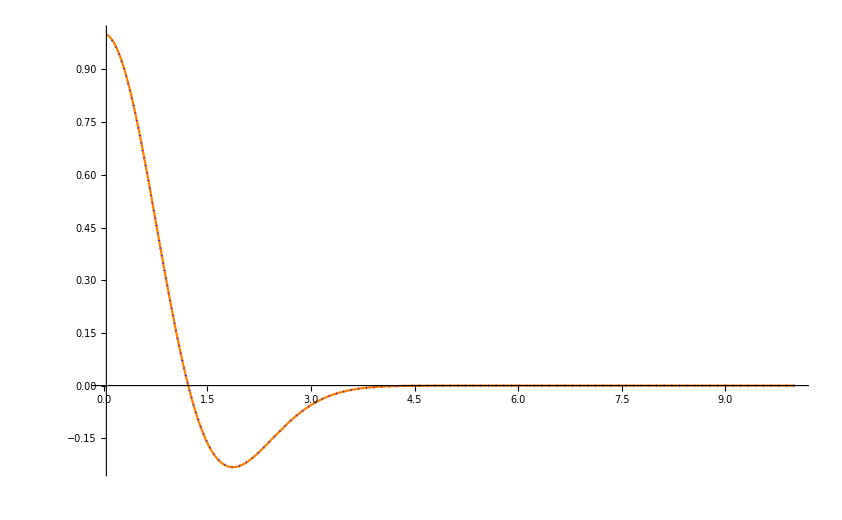

```mathematica
Plot[{y[x],LaguerreL[1,1/2,x^2]/LaguerreL[1,1/2,0] ⅇ^(-x^2/2)},{x,2h,10},PlotRange->Full,PlotStyle->{{Orange},{Blue,Dotted}}]
```

```mathematica
V=(δ(z-v^2)^2+m^2-δ v^4)z;
```

```mathematica
Normal[Series[D[V, z]-ω^2,{z,0,5}]]
```

m^2-4 v^2 z δ+3 z^2 δ-ω^2

```mathematica
Solve[Normal[Series[D[V, z]-ω^2,{z,0,5}]]==0,z]/.{δ->0.6,m->1,ω->0.7,v->1}
```

{{z→0.26528},{z→1.06805}}

```mathematica
Normal[Series[V,{z,0,5}]]
```

m^2 z-2 v^2 z^2 δ+z^3 δ

```mathematica
ClearAll["Global`*"]
```

```mathematica
monitoredFindRoot[args__] := Module[{s = 0, e = 0,j = 0},
{FindRoot[args, StepMonitor:>s++,EvaluationMonitor:>e++,Jacobian->{Automatic,EvaluationMonitor:>j++}],"Steps"->s,"Evaluations"->e,"Jacobian Evaluations"->j}]
```

```mathematica
QB[v_,δ_,ω_,α_,R_,n_]:=(
h=R/(n(*+1*));
a=0;
a1[x_]:=1;
a2[x_]:=2/x;
a3[x_]:=ω^2;
S[y_]:=(1-4 δ v^2 y^2+3δ y^4)y;
eq[0]=c[0]==3/2 α-c[1]/2;
(*eq[0]=(2/3 a3[0] h^2-6)c[0]+(6+(a3[0] h^2)/3) c[1]==h^2 S[2/3 c[0]+1/3 c[1]];*)
eq[-1]=c[-1]+4 c[0]+c[1]==6(y0-((y0 a3[0]-S[y0])h^2)/6);
Table[p[i]=6 a1[a+i h]-3h a2[a+i h]+h^2 a3[a+i h],{i,0,n}];
Table[q[i]=-12 a1[a+i h]+4 h^2 a3[a+i h],{i,0,n}];
Table[r[i]=6 a1[a+i h]+3h a2[a+i h]+h^2 a3[a+i h],{i,0,n}];
Table[eq[i]=p[i]c[i-1]+q[i]c[i]+r[i]c[i+1]==6 h^2 S[1/6 c[i-1]+2/3 c[i]+1/6 c[i+1]],{i,1,n}];
eq[n+1]=(1/6(√(1-ω^2)+1/R)-1/(2h))c[n-1]+2/3(√(1-ω^2)+1/R)c[n]+(1/6(√(1-ω^2)+1/R)+1/(2 h))c[n+1]==0;
sol=Table[c[k],{k,0,n+1}]/.FindRoot[Table[eq[i],{i,0,n+1}],Table[{c[k],v},{k,0,n+1}],WorkingPrecision->100];
(*coef=sol[[1]];*)
For[i=0,i≤n+1,i++,t[i]=sol[[i+2]]];
t[-1]=t[1];
(*Table[B[i][x_]:=Piecewise[{{0,x<a+(i-2) h},{(x-(a+(i-2)h))^3/(6 h^3),a+(i-2)h≤x<a+(i-1)h},{(-3(x-(a+(i-1)h))^3+3h(x-(a+(i-1)h))^2+3 h^2(x-(a+(i-1)h))+h^3)/(6 h^3),a+(i-1)h≤x<a+i h},{(3(x-(a+(i+1)h))^3+3h(x-(a+(i+1)h))^2-3 h^2(x-(a+(i+1)h))+h^3)/(6 h^3),a+i h≤x<a+(i+1)h},{(-(x-(a+(i+2)h))^3)/(6 h^3),a+(i+1)h≤x<a+(i+2)h},{0,x≥a+(i+2)h }}],{i,-1,n+1}];
y[x_]:=Sum[B[i][x]t[i],{i,-1,n+1}];*)
prof=Table[{(h+1) i,1/6 t[i-1]+2/3 t[i]+1/6 t[i+1]},{i,0,n}];
)
```

```mathematica
rmax[δ_,ω_]:=N[(√δ)/(2 √(1-δ))1/(ω-√(1-δ))];
ωmin[δ_,v_]:=√(1-δ v^4);
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
b[-1]=(h-δ)^3/(6 h^3);
b[0]=(-3(h-δ)^3+3(h-δ)^2 h+3(h-δ)h^2+h^3)/(6 h^3);
b[1]=(-3(δ)^3+3(δ)^2 h+3(δ)h^2+h^3)/(6 h^3);
b[2]=(δ)^3/(6 h^3);
Table[Expand[Simplify[2/δ D[b[i],δ]]],{i,-1,2}]
Table[db[i]=Expand[Simplify[D[b[i],δ]]],{i,-1,2}]
Table[ddb[i]=Expand[Simplify[D[b[i],{δ,2}]]],{i,-1,2}]
Simplify[(c1)db[-1]+c0 db[0]+c1 db[1]+c2 db[2]]
```

{2/h^2-1/(h δ)-δ/h^3,-4/h^2+(3 δ)/h^3,2/h^2+1/(h δ)-(3 δ)/h^3,δ/h^3}

{-1/(2 h)+δ/h^2-δ^2/(2 h^3),-(2 δ)/h^2+(3 δ^2)/(2 h^3),1/(2 h)+δ/h^2-(3 δ^2)/(2 h^3),δ^2/(2 h^3)}

{1/h^2-δ/h^3,-2/h^2+(3 δ)/h^3,1/h^2-(3 δ)/h^3,δ/h^3}

(δ (-4 c0 h+4 c1 h+3 c0 δ-4 c1 δ+c2 δ))/(2 h^3)

```mathematica
Series[Simplify[c1(D[b[-1],{δ,2}]+2/δ D[b[-1],δ]+(-δ^2+ϵ)b[-1])+c0(D[b[0],{δ,2}]+2/δ D[b[0],δ]+(-δ^2+ϵ)b[0])+c1(D[b[1],{δ,2}]+2/δ D[b[1],δ]+(-δ^2+ϵ)b[1])+c2(D[b[2],{δ,2}]+2/δ D[b[2],δ]+(-δ^2+ϵ)b[2])],{δ,0,2}]
```

(-18 c0+18 c1+2 c0 h^2 ϵ+c1 h^2 ϵ)/(3 h^2)+(2 (3 c0-4 c1+c2) δ)/h^3+((-2 c0 h^2-c1 h^2-3 c0 ϵ+3 c1 ϵ) δ^2)/(3 h^2)+O[δ]^3

```mathematica
solver3DHO2[R_,n_,α_,ϵ_]:=(
a=0;
h=R/n;
a1[x_]:=1;
a2[x_]:=2/x;
a3[x_]:=-x^2+ϵ;
f[x_]:=0;
eq[-1]=c[0]==3/2 α-c[1]/2;
eq[0]=(2/3 ϵ h^2-6)c[0]+(6+(ϵ h^2)/3) c[1]==0;
Table[p[i]=6 a1[a+i h]-3h a2[a+i h]+h^2 a3[a+i h],{i,1,n}];
Table[q[i]=-12 a1[a+i h]+4 h^2 a3[a+i h],{i,1,n}];
Table[r[i]=6 a1[a+i h]+3h a2[a+i h]+h^2 a3[a+i h],{i,1,n}];
Table[eq[i]=p[i]c[i-1]+q[i]c[i]+r[i]c[i+1]==0,{i,1,n}];
eq[n+1]=(-R/6+1/(2h))c[n-1]-(2R)/3 c[n]-(R/6+1/(2 h))c[n+1]==0;
sol=Table[c[k],{k,0,n+1}]/.NSolve[Table[eq[i],{i,-1,n+1}],Table[c[k],{k,-1,n+1}]]
(*coef=sol[[1]];*)
(*For[i=0,i≤n+1,i++,t[i]=coef[[i+1]]];
t[-1]=t[1];
Table[B[i][x_]:=Piecewise[{{0,x<a+(i-2) h},{(x-(a+(i-2)h))^3/(6 h^3),a+(i-2)h≤x<a+(i-1)h},{(-3(x-(a+(i-1)h))^3+3h(x-(a+(i-1)h))^2+3 h^2(x-(a+(i-1)h))+h^3)/(6 h^3),a+(i-1)h≤x<a+i h},{(3(x-(a+(i+1)h))^3+3h(x-(a+(i+1)h))^2-3 h^2(x-(a+(i+1)h))+h^3)/(6 h^3),a+i h≤x<a+(i+1)h},{(-(x-(a+(i+2)h))^3)/(6 h^3),a+(i+1)h≤x<a+(i+2)h},{0,x≥a+(i+2)h }}],{i,-1,n+1}];
y[x_]:=Sum[B[i][x]t[i],{i,-1,n+1}];
(*Plot[y[x],{x,0,R},PlotRange->Full]*)
ϕ=Table[{h i,1/6 t[i-1]+2/3 t[i]+1/6 t[i+1]},{i,0,n}];
(*ClearAll[a,h,a1,a2,a3,f,eq,t];*)*)
)
```

```mathematica
sol3DHO[R_,n_,α_,ϵ_]:=(
a=0;
h=R/n;
a1[x_]:=1;
a2[x_]:=2/x;
a3[x_]:=-x^2+ϵ;
f[x_]:=0;
Table[p[i]=(6 a1[i h]-3h a2[i h]+h^2 a3[i h])/(6 h^2),{i,1,n}];
Table[q[i]=(-12 a1[i h]+4 h^2 a3[i h])/(6 h^2),{i,1,n}];
Table[r[i]=(6 a1[i h]+3h a2[i h]+h^2 a3[i h])/(6 h^2),{i,1,n}];
Eq=Array[c,{n+3,n+3},{{-1,n+1},{-1,n+1}}];
For[i=-1,i≤n+1,i++,
If[i==1,c[-1,-1]=1,
If[i==-1,c[-1,1]=-1,
c[-1,i]=0;
];
];
];
For[i=-1,i≤n+1,i++,
If[i==0,c[0,0]=-6/h^2+2/3 ϵ,
If[(i==1)∨(i==-1),c[0,i]=(6/h^2+ϵ/3)/2,
c[0,i]=0;
];
];
];
For[i=1,i≤n,i++,
For[j=-1,j≤n+1,j++,
If[i==j,c[i,j]=q[i],
If[j==i-1,c[i,j]=p[i],
If[j==i+1,c[i,j]=r[i],
c[i,j]=0;
];
];
];
];
];
For[i=-1,i≤n+1,i++,c[n+1,i]=0];
c[n+1,n-1]=-R/6+1/(2 h);c[n+1,n]=(-2R)/3;c[n+1,n+1]=-(R/6+1/(2 h));
(*t=Eigenvectors[Eq][[1]];*)
(*coef=sol[[1]];*)
(*For[i=0,i≤n+1,i++,t[i]=coef[[i+1]]];
t[-1]=t[1];
Table[B[i][x_]:=Piecewise[{{0,x<a+(i-2) h},{(x-(a+(i-2)h))^3/(6 h^3),a+(i-2)h≤x<a+(i-1)h},{(-3(x-(a+(i-1)h))^3+3h(x-(a+(i-1)h))^2+3 h^2(x-(a+(i-1)h))+h^3)/(6 h^3),a+(i-1)h≤x<a+i h},{(3(x-(a+(i+1)h))^3+3h(x-(a+(i+1)h))^2-3 h^2(x-(a+(i+1)h))+h^3)/(6 h^3),a+i h≤x<a+(i+1)h},{(-(x-(a+(i+2)h))^3)/(6 h^3),a+(i+1)h≤x<a+(i+2)h},{0,x≥a+(i+2)h }}],{i,-1,n+1}];
y[x_]:=Sum[B[i][x]t[i],{i,-1,n+1}];*)
(*Plot[y[x],{x,0,R},PlotRange->Full]*)
(*ϕ=Table[{h i,1/6 t[i-1]+2/3 t[i+1]+1/6 t[i+1]},{i,2,n+2}];*)
(*ClearAll[a,h,a1,a2,a3,f,eq,t];*)
)
```

```mathematica
sol3DHO[6,30,1,7]
N[Det[Eq]]
N[Eigenvalues[Eq]]
```

4.38102×10^47

{-146.285,-105.121,-101.631,-99.1992,-97.4052,-95.5232,-93.1228,-90.2533,-86.9789,-83.3497,-79.4125,-75.214,-70.802,-66.2259,-61.5367,-56.7866,-52.0296,-47.3207,-42.7166,-38.2747,-34.0491,-30.0737,-26.3226,-22.6912,-19.0642,-15.3852,-11.6407,-7.82872,-4.75728,4.00522,-3.94843,0.967152,0.0106365}

```mathematica
MatrixForm[Eq]
```

(1 | 0 | -1 | 0 | 0 | 0 | 0 | 0
79/4 | -67/2 | 79/4 | 0 | 0 | 0 | 0 | 0
0 | 73/75 | -1291/150 | 2021/150 | 0 | 0 | 0 | 0
0 | 0 | 2411/600 | -1339/150 | 6161/600 | 0 | 0 | 0
0 | 0 | 0 | 739/150 | -473/50 | 682/75 | 0 | 0
0 | 0 | 0 | 0 | 6313/1200 | -1531/150 | 10063/1200 | 0
0 | 0 | 0 | 0 | 0 | 16/3 | -67/6 | 47/6
0 | 0 | 0 | 0 | 0 | 0 | 3149/600 | -617/50)

```mathematica
N[Det[Eq]]
```

7.7131×10^9

```mathematica
N[Eigenvalues[Eq]][[1]]
```

-34.3446

```mathematica
N[Eigenvectors[Eq,1][[1]]]
```

{-52.832,44899.1,-1867.33,323.557,-70.1796,16.7521,-4.19269,1.}

```mathematica
solver1DHO[R_,n_,α_,λ_,ϵ_]:=(
y0=1;
h=R/(n(*+1*));
a=0(*h*);
a1[x_]:=1;
a2[x_]:=0;
a3[x_]:=-λ/4(x^2-1/λ)^2+ϵ;
f[x_]:=0;
(*eq[-1]=1/6 c[1]+2/3 c[0]+1/6 c[-1]==α;*)
(*eq[0]=(2/3 ϵ h^2-6)c[0]+(6+(ϵ h^2)/3) c[1]==0;*)
eq[-1]=c[-1]+4 c[0]+c[1]==6α;
Table[p[i]=6 a1[a+i h]-3h a2[a+i h]+h^2 a3[a+i h],{i,0,n}];
Table[q[i]=-12 a1[a+i h]+4 h^2 a3[a+i h],{i,0,n}];
Table[r[i]=6 a1[a+i h]+3h a2[a+i h]+h^2 a3[a+i h],{i,0,n}];
Table[eq[i]=p[i]c[i-1]+q[i]c[i]+r[i]c[i+1]==0,{i,0,n}];
eq[n+1]=(-R/6+1/(2h))c[n-1]-(2R)/3 c[n]-(R/6+1/(2 h))c[n+1]==0;
sol=Table[c[k],{k,-1,n+1}]/.NSolve[Table[eq[i],{i,-1,n+1}],Table[c[k],{k,-1,n+1}]];
coef=sol[[1]];
For[i=-1,i≤n+1,i++,t[i]=coef[[i+2]]];
(*t[-1]=t[1];*)
Table[B[i][x_]:=Piecewise[{{0,x<a+(i-2) h},{(x-(a+(i-2)h))^3/(6 h^3),a+(i-2)h≤x<a+(i-1)h},{(-3(x-(a+(i-1)h))^3+3h(x-(a+(i-1)h))^2+3 h^2(x-(a+(i-1)h))+h^3)/(6 h^3),a+(i-1)h≤x<a+i h},{(3(x-(a+(i+1)h))^3+3h(x-(a+(i+1)h))^2-3 h^2(x-(a+(i+1)h))+h^3)/(6 h^3),a+i h≤x<a+(i+1)h},{(-(x-(a+(i+2)h))^3)/(6 h^3),a+(i+1)h≤x<a+(i+2)h},{0,x≥a+(i+2)h }}],{i,-1,n+1}];
y[x_]:=Sum[B[i][x]t[i],{i,-1,n+1}];
(*Plot[y[x],{x,0,R},PlotRange->Full]*)
ϕ=Table[{h i,1/6 t[i-1]+2/3 t[i]+1/6 t[i+1]},{i,0,n}];
(*ClearAll[a,h,a1,a2,a3,f,eq,t];*)
)
```

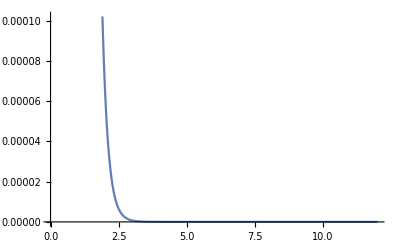

```mathematica
solver1DHO[18,3000,1,0.01,0.994996]
ListLinePlot[Table[{ϕ[[i,1]],ϕ[[i,2]]},{i,1,2000}]]
```

```mathematica
1/(√0.03)
```

5.7735

```mathematica
0.03^3
```

0.000027

```mathematica
D[λ(x^2-η^2)^2,{x,2}]
```

(8 x^2+4 (x^2-η^2)) λ

```mathematica
Egs[λ_]:=1-8 √(1/(λ π))ⅇ^(-2/(3λ)) -λ/2
```

```mathematica
Egs[0.1]
```

0.931836

```mathematica
0.9949955805826176
```